```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,δ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ*c/k* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ*c/k* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -ρ*H[t]*R[t] -δ*H[t]- β*F[t],
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
```

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/7B[n],B[1]==1*10^(-7)},B,{n,1,75}]]
```

{1.×10^-7,1.14286×10^-7,1.30612×10^-7,1.49271×10^-7,1.70596×10^-7,1.94966×10^-7,2.22819×10^-7,2.5465×10^-7,2.91029×10^-7,3.32604×10^-7,3.80119×10^-7,4.34422×10^-7,4.96482×10^-7,5.67408×10^-7,6.48466×10^-7,7.41104×10^-7,8.46976×10^-7,9.67973×10^-7,1.10625×10^-6,1.26429×10^-6,1.4449×10^-6,1.65132×10^-6,1.88722×10^-6,2.15682×10^-6,2.46494×10^-6,2.81708×10^-6,3.21952×10^-6,3.67945×10^-6,4.20508×10^-6,4.80581×10^-6,5.49235×10^-6,6.27697×10^-6,7.17369×10^-6,8.1985×10^-6,9.36971×10^-6,0.0000107082,0.000012238,0.0000139863,0.0000159843,0.0000182678,0.0000208775,0.00002386,0.0000272685,0.000031164,0.000035616,0.000040704,0.0000465189,0.0000531645,0.0000607594,0.0000694393,0.0000793592,0.0000906962,0.000103653,0.00011846,0.000135383,0.000154724,0.000176827,0.000202088,0.000230958,0.000263952,0.000301659,0.000344754,0.000394004,0.00045029,0.000514618,0.000588134,0.000672154,0.000768175,0.000877915,0.00100333,0.00114666,0.00131047,0.00149768,0.00171164,0.00195616}

```mathematica
(*Don't go above 0.008457893893047288*)
```

```mathematica
Quiet[(
sigvalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-8)},B,{n,1,43}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^2;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=(μ (-λ+σ))/(2 λ ρ+μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::nderr: Error test failure at t == 2.62076×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {2630000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 2.58182×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 2.52472×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.65795×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.14776×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.39932×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.25698×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9260000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.15132×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.31377×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.70921×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7710000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.22152×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.96608×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.54437×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {5550000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.31666×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.5968×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.77174×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.74288×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.29774×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.07182×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.23593×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.74713×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.75291×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.06356×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.21295×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.6603×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9670000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.39698×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.94354×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.70689×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9710000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.79922×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.21298×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.19535×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7200000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.02174×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.69751×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.14383×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9150000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 3.0601×10^9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {9150000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.44855×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.24725×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.61797×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.36044×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.71343×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9720000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.78001×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.83472×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.63392×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8640000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.81933×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.10018×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.87206×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9880000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.18697×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.5977×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.3623×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9370000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.66371×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.16016×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

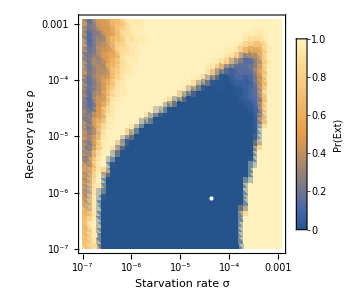

```mathematica
ExtPlot=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}
```

{Log[-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])],Log[-(1.67857×10^-6)/(M^(1/4) Log[0.292893/(1-0.707107 (1-0.0202 M^0.19)^(1/4))])]}

```mathematica
Starvation
```

0.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2.pdf"}],ExtPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2.pdf

```mathematica
threshold =(N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality})*0.2/.M->Mass
```

16.6738

```mathematica
Mass
```

10

```mathematica
ts=Table[t,{t,0,100000000,100000}];
```

```mathematica
ts[[5]]
```

400000

```mathematica
ts[[1001]]
```

100000000

```mathematica
4*10^5
```

400000

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]]
```

{4.×10^-6,5.×10^-6,6.25×10^-6,7.8125×10^-6,9.76563×10^-6,0.000012207,0.0000152588,0.0000190735,0.0000238419,0.0000298023,0.0000372529,0.0000465661,0.0000582077,0.0000727596,0.0000909495,0.000113687,0.000142109,0.000177636,0.000222045,0.000277556,0.000346945,0.000433681,0.000542101,0.000677626,0.000847033,0.00105879,0.00132349,0.00165436,0.00206795,0.00258494,0.00323117,0.00403897,0.00504871,0.00631089,0.00788861,0.00986076,0.012326,0.0154074,0.0192593,0.0240741,0.0300927,0.0376158,0.0470198,0.0587747,0.0734684,0.0918355,0.114794,0.143493,0.179366,0.224208}

```mathematica
(*For M=1000*)
```

```mathematica
Quiet[(
sigvalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-8)},B,{n,1,43}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^3;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::nderr: Error test failure at t == 1.48159×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {1490000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.01316×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.73564×10^9; unable to continue.

NDSolve::ndsz: At t == 6.1915×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.25327×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 6.41765×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.34753×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {650000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {650000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 6.00305×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.019×10^8, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {70000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 5.46937×10^8, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {70000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {70000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 6.65753×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.08597×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 1.16167×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 1.11244×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.24295×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 4.634×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 4.69288×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 5.0904×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

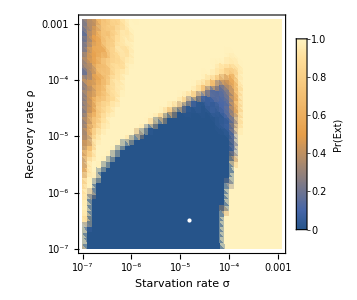

```mathematica
ExtPlot103=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_103.pdf"}],ExtPlot103,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_103.pdf

```mathematica
(*For M=10^6*)
```

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/2B[n],B[1]==1*10^(-8)},B,{n,1,25}]]
```

{1.×10^-8,1.5×10^-8,2.25×10^-8,3.375×10^-8,5.0625×10^-8,7.59375×10^-8,1.13906×10^-7,1.70859×10^-7,2.56289×10^-7,3.84434×10^-7,5.7665×10^-7,8.64976×10^-7,1.29746×10^-6,1.9462×10^-6,2.91929×10^-6,4.37894×10^-6,6.56841×10^-6,9.85261×10^-6,0.0000147789,0.0000221684,0.0000332526,0.0000498789,0.0000748183,0.000112227,0.000168341}

```mathematica
Quiet[(
sigvalues =   N[RecurrenceTable[{B[n+1] == B[n]+1/6B[n],B[1]==1*10^(-8)},B,{n,1,61}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^6;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 25;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::ndsz: At t == 6.60871×10^8, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {670000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.35339×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.35506×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 1.38252×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 1.41401×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.87442×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.49538×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9500000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.54984×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.68013×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.23014×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.00868×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.95922×10^9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2960000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 3.01849×10^9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2960000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2960000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.81911×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.63711×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.98787×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.10815×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7110000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.36798×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.07052×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.41333×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.34168×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.28577×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.42246×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 5.76105×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.26727×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7270000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.85178×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.56946×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.23179×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9240000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.51081×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.22212×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.69915×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.8457×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.54025×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.78427×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.66304×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.41847×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.80922×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7810000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.49587×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.12999×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.7371×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.10767×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.14866×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.53961×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8540000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.32265×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.28825×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.56181×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.48915×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.97701×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.48127×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9490000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.97753×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.80873×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.70258×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {8710000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.37009×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.50725×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.58863×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9590000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.32429×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.69108×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

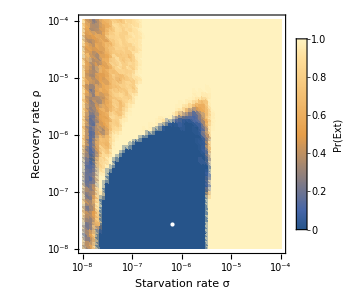

```mathematica
ExtPlot106=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_106.pdf"}],ExtPlot106,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_106.pdf